```mathematica
Clear["`*"]
SetDirectory[NotebookDirectory[]]
```

/Users/yinshi/Documents/work/post-doc-Humboldt/github/work/critical_region/cheby/LPA/v9/mub0Tc/buffer

```mathematica
(*list0=Flatten[Import["a.dat"]];*)
k=Flatten[Import["k.dat"]];
list=Partition[Flatten[Import["bk.dat"]],51];
```

```mathematica
list1=Table[Rest[list[[i]]],{i,1,Length[k]}];
```

```mathematica
ρmin=0.;
ρmax=30000.;
c0=1.85*10^6;
fpi=93.5;
cmax=10.^7;
cmin=10.^-2;
```

```mathematica
(*rhoend=80;
eqn6=Table[Evaluate[(test=SetPrecision[Sum[list1[[n]]*Cos[n*ArcCos[(2ρ-ρmin-ρmax)/(ρmax-ρmin)]],{n,1,50}]+1/2 First[list1],52])],{ρ,0,rhoend,rhoend/191}];
sigma=Table[√(2 rho),{rho,0,rhoend,rhoend/191}];*)
```

```mathematica
(*ListPlot[Transpose[{sigma,eqn6-eqn6[[1]]+10^7}],PlotRange->{{0,11},All},ScalingFunctions->{Automatic,"Log"}]*)
```

```mathematica
rhoend=80;
eqn7=Table[Table[Evaluate[Re[(test=SetPrecision[Sum[list1[[i]][[n]]*Cos[n*ArcCos[(2ρ-ρmin-ρmax)/(ρmax-ρmin)]],{n,1,50}]+1/2 First[list[[i]]],52])]],{ρ,0,0,rhoend/2000}],{i,1,Length[k]}];
(*sigma=Table[√(2 rho),{rho,0,rhoend,rhoend/2000.}];*)
```

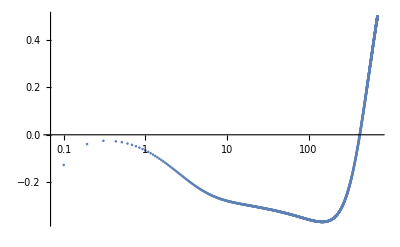

```mathematica
ListPlot[Transpose[{k,Flatten[eqn7]/k^2}],PlotRange->All,ScalingFunctions->{"Log",Automatic}]
```